1.05267

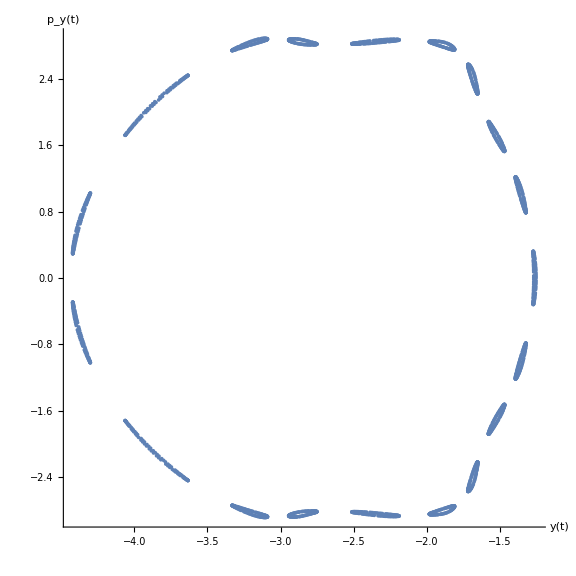

```mathematica
(*Codigo sencillo que halla, aproximadamente, el winding number de cierta resonancia*)
mu = 0.8;
l = {-1.8677769989109176,1.0225792001563434,-3.944123543145011,-3.230586304881678};
I1 = 1/2(l[[3]]^2 + l[[1]]^2);
I2 = 1/2(l[[4]]^2 + l[[2]]^2);
WindN = (1 + I1 + mu*I2)/(1 + I2 + mu*I1) (*Winding number*)
abc={x'[t]== z[t] + 0.5*z[t]*(z[t]^2 + x[t]^2),y'[t]== w[t] + 0.5*w[t]*(w[t]^2 + y[t]^2), z'[t]== -x[t]*(1 + 2*mu*y[t]^2 +  0.5*(z[t]^2 + x[t]^2)),w'[t]==-y[t]*(1 + 2*mu*x[t]^2 + 0.5*(w[t]^2 + y[t]^2))};
psect[{x0_,y0_,z0_,w0_}]:=Reap[NDSolve[{abc,x[0]==x0,y[0]==y0,z[0]==z0,w[0]==w0,WhenEvent[x[t]==0&&z[t]>0,Sow[{y[t],w[t]}]]},{x[t],y[t],z[t],w[t]},{t,0,1000},MaxSteps->Infinity]][[-1,1]]

abcdata=Map[psect,{{l[[1]],l[[2]],l[[3]],l[[4]]}}];

ListPlot[abcdata,ImageSize->Large, AspectRatio->1,AxesLabel->{Style["y(t)", Bold,20,Black], Style["p_y(t)", Bold,20,Black]}]
```